Solution to equation according to the book by G.Strang using hat functions:

```mathematica
h=1/3;
```

```mathematica
Clear[ϕ1,ϕ2,ϕ3]
```

```mathematica
ϕ1[x_]:= Piecewise[{{x/h,0≤ x≤ h},{2-x/h,h≤ x ≤2h}}];
ϕ2[x_]:= Piecewise[{{x/h-1,h≤ x≤ 2h},{3-x/h,2h<=x ≤3h}}];
ϕ3[x_]:= Piecewise[{{x/h-2,2h≤ x≤ 3h},{0,_}}];
```

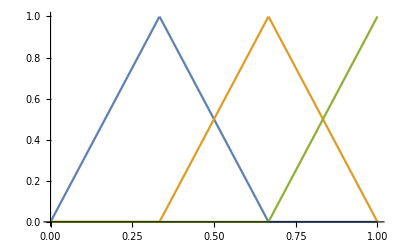

```mathematica
Plot[{ϕ1[x],ϕ2[x],ϕ3[x]},{x,0,1}]
```

```mathematica
ϕ3[2h]
```

0

We are solving  equation KU = F , where F = ∫V_1dx as V is equal to vector ϕ we can calculate F:

```mathematica
ϕ={ϕ1[x],ϕ2[x],ϕ3[x]};
F =Integrate[ϕ,{x,0,1}];
```

For stiffness matrix Kij we have if the c(x) = 1, K=∫V’(x)ϕ’(x)dx as V is equal to ϕ:

```mathematica
dϕ = D[ϕ,{x}];
Km = Outer[Times,dϕ,dϕ];
```

```mathematica
K=Integrate[Km,{x,0,1}];
```

Final solution is given by inverse U = K^-1 F

```mathematica
U=Inverse[K].F
```

{5/18,4/9,1/2}

Exact solution to this problem is:

```mathematica
Clear[u]
```

```mathematica
u[x_]:=x-1/2 x^2;
```

Error of the solution is :

```mathematica
x = {h,2h,3h};
U -Map[u[#]&,x]
```

{0,0,0}

We get exact solution at the nodes!!